```mathematica
ClearAll["Global`*"]
```

```mathematica
N[100^ZetaZero[1]/(ZetaZero[1] Zeta'[ZetaZero[1]])]
```

0.751611+0.479272 ⅈ

```mathematica
Sum[ N[Floor[100/j]^ZetaZero[1]/(ZetaZero[1] Zeta'[ZetaZero[1]])],{j,2,100}]
```

-1.09186-1.9303 ⅈ

```mathematica
N[100^ZetaZero[1]/(ZetaZero[1])]
```

0.528969+0.469138 ⅈ

```mathematica
Sum[ N[Floor[100/j]^ZetaZero[1]/(ZetaZero[1] )],{j,2,100}]
```

-0.614543-1.64816 ⅈ

```mathematica
LL[n_] := Sum[ Log[j]-LL[Floor[n/j]],{j,2,n}]
MM[n_] :=1-Sum[MM[Floor[n/j]],{j,2,n}]
L2[n_] := Sum[ Log[j]MM[Floor[n/j]],{j,2,n}]
E2b[n_,k_, a_]:= E2b[n,k,a]=Sum[ E2b[n/j,k-1,a],{j,2,n}]-a Sum[ E2b[n/(a j),k-1,a],{j,1,n/a}];E2b[n_,0,a_]:=1
D1c[n_, k_, b_] := Sum[ Binomial[k+j-1,k-1] b^j 
Sum[FactorialPower[k,a]/a! E2b[n/b^j,a,b],{a,0,Log[If[b>2,2,b],n/b^j]}],{j,0,Log[b,n]}]
D1a[n_, k_, b_,r1_,r2_] := Sum[ Binomial[k+j-1,k-1] b^j 
Sum[FactorialPower[k,a]/a! E2b[n/b^j,a,b],{a,0,Log[If[b>2,2,b],n/b^j]}],{j,r1,r2}]
L3[n_,a_] := Sum[Log[j] D1c[Floor[n/j],-1,a],{j,2,n}]
M2[n_,a_]:=Sum[(-1)^k( E2b[n,k,a]-a E2b[n/a,k,a]),{k,0,Log[a,n]}]
L6[n_,a_] := Sum[Log[j] M2[Floor[n/j],a],{j,2,n/2}]+Sum[Log[j] ,{j,n/2+1,n}]
```

```mathematica
N[L3[100,1.5]]
```

94.0453

```mathematica
N[L6[100,1.5]]
```

94.0453

```mathematica
N[LL[100]]
```

94.0453

```mathematica
(-1)^0( E2b[10,0,3]-3 E2b[10/3,0,3])
```

-2

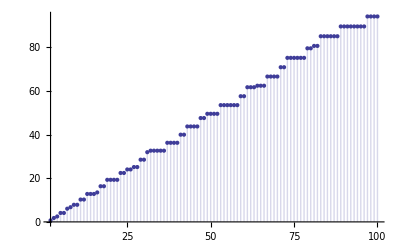

```mathematica
DiscretePlot[LL[n],{n,2,100}]
```

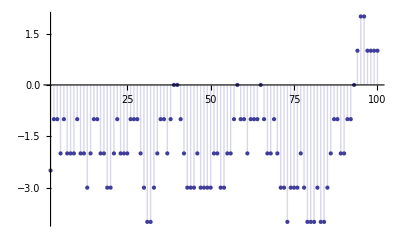

```mathematica
DiscretePlot[M2[n,2.5],{n,2,100}]
```

```mathematica
DiscretePlot[L2[n],{n,2,100}]
```

-Graphics-

```mathematica
Series[(x+1)^-2,{x,0,20}]
```

1-2 x+3 x^2-4 x^3+5 x^4-6 x^5+7 x^6-8 x^7+9 x^8-10 x^9+11 x^10-12 x^11+13 x^12-14 x^13+15 x^14-16 x^15+17 x^16-18 x^17+19 x^18-20 x^19+21 x^20+O[x]^21

```mathematica
f[n_, k_] := 1-(k+1)Sum[ f[Floor[n/j],k+1],{j,2,n}]
```

```mathematica
f[100,1]
```

14365

```mathematica
MM[n_,k_] := Sum[ MoebiusMu[ j]MM[Floor[n/j],k-1],{j,1,n}];MM[n_,0]:=1
```

```mathematica
MM[100,2]
```

19

```mathematica
D2[n_,k_]:=Sum[D2[Floor[n/j],k-1],{j,2,n}];D2[n_,0]:=1
DA[n_,z_]:=Sum[FactorialPower[z,a]/a! D2[n,a],{a,0,Log[2,n]}]
da[n_,z_]:=Sum[FactorialPower[z,a]/a!d2[n,a],{a,0,Log[2,n]}]
```

```mathematica
DA[100,-2]
```

19

```mathematica
da[100,-2]
```

d2[100,0]-2 d2[100,1]+3 d2[100,2]-4 d2[100,3]+5 d2[100,4]-6 d2[100,5]+7 d2[100,6]

```mathematica
Table[{n,MM[n],M2[n,1.5],D1c[n,-1,1.5]},{n,0,100}]//TableForm
```

0 | 1 | 0. | 0.
1 | 1 | -0.5 | 1.
2 | 0 | 0. | 0.
3 | -1 | -1. | -1.
4 | -1 | -1. | -1.
5 | -2 | -2. | -2.
6 | -1 | -1. | -1.
7 | -2 | -2. | -2.
8 | -2 | -2. | -2.
9 | -2 | -2. | -2.
10 | -1 | -1. | -1.
11 | -2 | -2. | -2.
12 | -2 | -2. | -2.
13 | -3 | -3. | -3.
14 | -2 | -2. | -2.
15 | -1 | -1. | -1.
16 | -1 | -1. | -1.
17 | -2 | -2. | -2.
18 | -2 | -2. | -2.
19 | -3 | -3. | -3.
20 | -3 | -3. | -3.
21 | -2 | -2. | -2.
22 | -1 | -1. | -1.
23 | -2 | -2. | -2.
24 | -2 | -2. | -2.
25 | -2 | -2. | -2.
26 | -1 | -1. | -1.
27 | -1 | -1. | -1.
28 | -1 | -1. | -1.
29 | -2 | -2. | -2.
30 | -3 | -3. | -3.
31 | -4 | -4. | -4.
32 | -4 | -4. | -4.
33 | -3 | -3. | -3.
34 | -2 | -2. | -2.
35 | -1 | -1. | -1.
36 | -1 | -1. | -1.
37 | -2 | -2. | -2.
38 | -1 | -1. | -1.
39 | 0 | 0. | 0.
40 | 0 | 0. | 0.
41 | -1 | -1. | -1.
42 | -2 | -2. | -2.
43 | -3 | -3. | -3.
44 | -3 | -3. | -3.
45 | -3 | -3. | -3.
46 | -2 | -2. | -2.
47 | -3 | -3. | -3.
48 | -3 | -3. | -3.
49 | -3 | -3. | -3.
50 | -3 | -3. | -3.
51 | -2 | -2. | -2.
52 | -2 | -2. | -2.
53 | -3 | -3. | -3.
54 | -3 | -3. | -3.
55 | -2 | -2. | -2.
56 | -2 | -2. | -2.
57 | -1 | -1. | -1.
58 | 0 | 0. | 0.
59 | -1 | -1. | -1.
60 | -1 | -1. | -1.
61 | -2 | -2. | -2.
62 | -1 | -1. | -1.
63 | -1 | -1. | -1.
64 | -1 | -1. | -1.
65 | 0 | 0. | 0.
66 | -1 | -1. | -1.
67 | -2 | -2. | -2.
68 | -2 | -2. | -2.
69 | -1 | -1. | -1.
70 | -2 | -2. | -2.
71 | -3 | -3. | -3.
72 | -3 | -3. | -3.
73 | -4 | -4. | -4.
74 | -3 | -3. | -3.
75 | -3 | -3. | -3.
76 | -3 | -3. | -3.
77 | -2 | -2. | -2.
78 | -3 | -3. | -3.
79 | -4 | -4. | -4.
80 | -4 | -4. | -4.
81 | -4 | -4. | -4.
82 | -3 | -3. | -3.
83 | -4 | -4. | -4.
84 | -4 | -4. | -4.
85 | -3 | -3. | -3.
86 | -2 | -2. | -2.
87 | -1 | -1. | -1.
88 | -1 | -1. | -1.
89 | -2 | -2. | -2.
90 | -2 | -2. | -2.
91 | -1 | -1. | -1.
92 | -1 | -1. | -1.
93 | 0 | 0. | 0.
94 | 1 | 1. | 1.
95 | 2 | 2. | 2.
96 | 2 | 2. | 2.
97 | 1 | 1. | 1.
98 | 1 | 1. | 1.
99 | 1 | 1. | 1.
100 | 1 | 1. | 1.

```mathematica
D1cc[n_, k_, b_] := Sum[ Binomial[k+j-1,k-1] b^j 
Sum[FactorialPower[k,a]/a! E2[n/b^j,a,b],{a,0,Log[If[b>2,2,b],n/b^j]}],{j,0,Log[b,n]}]
```

```mathematica
D1cc[1,-1,2]
```

E2[1,0,2]

```mathematica
M2d[n_,a_]:=Sum[(-1)^k( E2[n,k,a]-a E2[n/a,k,a]),{k,0,Log[a,n]}]
```

```mathematica
M2d[1,a]
```

E2[1,0,a]-a E2[1/a,0,a]

```mathematica
E2b[n_,k_, a_]:= E2b[n,k,a]=Sum[ E2b[n/j,k-1,a],{j,2,n}]-a Sum[ E2b[n/(a j),k-1,a],{j,1,n/a}];E2b[n_,0,a_]:=1
```

```mathematica
E2b[200,2,3]
```

9

```mathematica
Et2[n_,a_] := Sum[ 1, {j,2,n},{k,2,n/j}]-2a Sum[ 1, {j,2,n},{k,1,n/(j a)}]+a^2Sum[1,{j,1,n/a},{k,1,n/(a^2 j)}]
```

```mathematica
Et2[200,3]
```

9

```mathematica
Et3[n_,a_] := Sum[ 1, {j,2,n},{k,2,n/j},{l,2,n/(j k)}]-3a Sum[ 1, {j,2,n},{k,2,n/j},{l,1,n/(a j k)}]+3 a^2Sum[1,{j,2,n},{k,1,n/(a j)},{l,1,n/(j k a^2)}]- a^3Sum[1,{j,1,n/a},{k,1,n/(a^2 j)},{l,1,n/(a^3 j k)}]
```

```mathematica
Et3[200,4]
```

51

```mathematica
E2b[200,3,4]
```

51

```mathematica
Table[{n, E2b[n,rr=3,aa=1.00000000000001]-E2b[n-1,rr,aa]},{n,2,100}]//TableForm
```

2 | -1.
3 | -3.04201×10^-14
4 | -2.9754×10^-14
5 | -2.93099×10^-14
6 | -2.88658×10^-14
7 | -3.28626×10^-14
8 | 1.
9 | -1.
10 | -3.19744×10^-14
11 | -2.66454×10^-14
12 | 3.
13 | -3.
14 | -2.66454×10^-14
15 | -3.37508×10^-14
16 | 3.
17 | -3.
18 | 3.
19 | -3.
20 | 3.
21 | -3.
22 | -3.55271×10^-14
23 | -3.19744×10^-14
24 | 9.
25 | -9.
26 | -2.4869×10^-14
27 | 1.
28 | 2.
29 | -3.
30 | 6.
31 | -6.
32 | 6.
33 | -6.
34 | -1.77636×10^-14
35 | -3.55271×10^-14
36 | 12.
37 | -12.
38 | -2.13163×10^-14
39 | -1.42109×10^-14
40 | 9.
41 | -9.
42 | 6.
43 | -6.
44 | 3.
45 | -4.26326×10^-14
46 | -3.
47 | -4.9738×10^-14
48 | 18.
49 | -18.
50 | 3.
51 | -3.
52 | 3.
53 | -3.
54 | 9.
55 | -9.
56 | 9.
57 | -9.
58 | -2.13163×10^-14
59 | -3.55271×10^-14
60 | 21.
61 | -21.
62 | -4.26326×10^-14
63 | 3.
64 | 7.
65 | -10.
66 | 6.
67 | -6.
68 | 3.
69 | -3.
70 | 6.
71 | -6.
72 | 27.
73 | -27.
74 | 0.
75 | 3.
76 | -2.84217×10^-14
77 | -3.
78 | 6.
79 | -6.
80 | 18.
81 | -15.
82 | -3.
83 | -5.68434×10^-14
84 | 21.
85 | -21.
86 | -5.68434×10^-14
87 | 1.42109×10^-14
88 | 9.
89 | -9.
90 | 21.
91 | -21.
92 | 3.
93 | -3.
94 | 1.42109×10^-14
95 | -5.68434×10^-14
96 | 30.
97 | -30.
98 | 3.
99 | -5.68434×10^-14
100 | 9.

```mathematica
d2[n_,k_]:=Sum[d2[j,k-1] d2[n/j,1],{j,Divisors[n]}];d2[n_,1]:=1;d2[1,1]:=0;d2[n_,0]:=0;d2[1,0]:=1
```

```mathematica
Table[{n, d2[n,4],E2b[n,rr=4,aa=1.000000001]-aa E2b[n/aa,rr,aa]},{n,1,100}]//TableForm
```

1 | 0 | 0.
2 | 0 | -1.×10^-9
3 | 0 | -1.×10^-9
4 | 0 | -1.×10^-9
5 | 0 | -1.×10^-9
6 | 0 | -1.×10^-9
7 | 0 | -1.×10^-9
8 | 0 | -1.×10^-9
9 | 0 | -1.×10^-9
10 | 0 | -1.×10^-9
11 | 0 | -1.×10^-9
12 | 0 | -1.×10^-9
13 | 0 | -1.×10^-9
14 | 0 | -1.×10^-9
15 | 0 | -1.×10^-9
16 | 1 | 1.
17 | 0 | -1.×10^-9
18 | 0 | -1.×10^-9
19 | 0 | -1.×10^-9
20 | 0 | -1.×10^-9
21 | 0 | -1.×10^-9
22 | 0 | -1.×10^-9
23 | 0 | -1.×10^-9
24 | 4 | 4.
25 | 0 | -1.×10^-9
26 | 0 | -1.×10^-9
27 | 0 | -1.×10^-9
28 | 0 | -1.×10^-9
29 | 0 | -1.×10^-9
30 | 0 | -1.×10^-9
31 | 0 | -1.×10^-9
32 | 4 | 4.
33 | 0 | -1.×10^-9
34 | 0 | -1.×10^-9
35 | 0 | -1.×10^-9
36 | 6 | 6.
37 | 0 | -1.×10^-9
38 | 0 | -1.×10^-9
39 | 0 | -1.×10^-9
40 | 4 | 4.
41 | 0 | -1.×10^-9
42 | 0 | -1.×10^-9
43 | 0 | -1.×10^-9
44 | 0 | -1.×10^-9
45 | 0 | -1.×10^-9
46 | 0 | -1.×10^-9
47 | 0 | -1.×10^-9
48 | 16 | 16.
49 | 0 | -1.×10^-9
50 | 0 | -1.×10^-9
51 | 0 | -1.×10^-9
52 | 0 | -1.×10^-9
53 | 0 | -1.×10^-9
54 | 4 | 4.
55 | 0 | -1.×10^-9
56 | 4 | 4.
57 | 0 | -1.×10^-9
58 | 0 | -1.×10^-9
59 | 0 | -1.×10^-9
60 | 12 | 12.
61 | 0 | -1.×10^-9
62 | 0 | -1.×10^-9
63 | 0 | -1.×10^-9
64 | 10 | 10.
65 | 0 | -1.×10^-9
66 | 0 | -1.×10^-9
67 | 0 | -1.×10^-9
68 | 0 | -1.×10^-9
69 | 0 | -1.×10^-9
70 | 0 | -1.×10^-9
71 | 0 | -1.×10^-9
72 | 28 | 28.
73 | 0 | -1.×10^-9
74 | 0 | -1.×10^-9
75 | 0 | -1.×10^-9
76 | 0 | -1.×10^-9
77 | 0 | -1.×10^-9
78 | 0 | -1.×10^-9
79 | 0 | -1.×10^-9
80 | 16 | 16.
81 | 1 | 1.
82 | 0 | -1.×10^-9
83 | 0 | -1.×10^-9
84 | 12 | 12.
85 | 0 | -1.×10^-9
86 | 0 | -1.×10^-9
87 | 0 | -1.×10^-9
88 | 4 | 4.
89 | 0 | -1.×10^-9
90 | 12 | 12.
91 | 0 | -1.×10^-9
92 | 0 | -1.×10^-9
93 | 0 | -1.×10^-9
94 | 0 | -1.×10^-9
95 | 0 | -1.×10^-9
96 | 40 | 40.
97 | 0 | -1.×10^-9
98 | 0 | -1.×10^-9
99 | 0 | -1.×10^-9
100 | 6 | 6.

```mathematica
M2[30,1.1]
```

-3.

```mathematica
MM[30]
```

-3

```mathematica
$RecursionLimit=10000
```

10000

```mathematica
Table[(-1)^k( E2b[30,k,aa=1.01]-aa E2b[30/aa,k,aa]),{k,0,Log[1.01,30]}]//TableForm
```

$Aborted[]

```mathematica
Table[
{5/1.01^j,D1a[5,1,1.01,j,j]},{j,0,Log[1.01,5]}]//TableForm
```

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$Aborted

```mathematica
E2b[10,2,1.001]
```

3.01802

```mathematica
8-2 1.001 14 + 1.001 1.001 23
```

3.01802